第34回年次大会予稿

# 地域研究活動の指標開発にむけて - 文書からの地名抽出 -

# Towards the development of indicators for regional studies - Extraction of place names from documents -

黄秋実^1，寺田将春^1，上村麻里亜^1，船守美穂^1，天野晃^1

^1鹿児島大学

要旨：
近年我が国では、多くの地域において少子高齢化や人口流出により労働人口が減少し、地域課題の解決が困難になりつつある。これに対し、文部科学省は地方大学にその解決への取り組みを期待している面がある。実際、多くの大学も自身の存在意義を示すために地域に根ざした研究に力を入れている。一方で、計量書誌学の観点からは、このような地域研究の活動を示すような指標の開発はあまり見られない。これにはいくつかの問題があるからだと思われる。まず、地域の名称（地名）を文章等から正しく抽出することが困難であり、つぎにその地名が唯一に決められるかも難しい問題である。最終的には対象となる論文やデータに対して地名や地理情報をユニークに紐づける（キュレーションする）仕組みが必要となるであろう。本研究では、このようなソリューションを視野に入れるものの、まずは地名の抽出精度に着目し、コンパクトなテストデータを用いた試みを行う。

## 背景

本学では、2025年4月にオープンサイエンス研究開発部門が附属図書館の下部組織として発足した[1]。当部門は、学内外の組織との協力・協調のもとに地域課題解決を目指す「KAGOSHIMAモデル」[2]を推進するための中心的な部局である。地方大学である本学では、地域社会への貢献は重要な任務であるものの、その成果をどのように発信あるいは見える化するかもまた、重要な課題となっている。このような社会活動・社会貢献にかかる指標開発や分析は、活動そのものを把握し、より効果的に推進するためにも重要なものとなる。本部門ではこのための試験的な活動の一環として、ドキュメントから固有表現を抽出しその関係性を整理する仕組みの開発を予定しており、その第一段階としてAIを導入した地域（地名）を対象とした固有表現抽出（NER）の試みとその評価を行った。

## マテリアル・方法

まず、KAKENデータベース[3]より、国立大学によるレポートを収集した。本研究ではこのうちからランダムに選択した4大学の報告書からさらにランダムに各50件を抽出し、対象とした。地域名の抽出対象は研究課題名と報告書本文とした。

次にmecabにより形態素解析を行い、”固有名詞”および”地域”のラベルがあるものを抽出した。これらに対し、さらにmecabの判定が妥当かを判定者に判定させた。判定者は3種のAIと3名の人とした。

判定者へは、AI、人ともに表1の指示を与えた。データはJSON形式で与え、第２要素を抽出された地域名、第４要素をタイトルおよび本文とした。それ以外の要素は管理目的で挿入したものであり無視するよう促した。なお、AIには、Gemma3（4b）、Lamma3（8b）、Qwen3（32b）を用いた。

表1

添付のデータに対して以下の作業を行って下さい。
 
 - 概要 : 地名候補を地名であるか判定する。
 - 入力データ形式 : json形式、4 つの要素から成る。各要素はさらに配列である可能性がある。
 - 入力データの各要素の説明 : 
  - 第1要素 : 無視して良い
  - 第2要素 : 第4要素から抽出された地名候補
  - 第3要素 : 無視して良い
  - 第4要素 : 文章 （配列）
- 行ってほしい作業 : jsonの第2要素の各地名候補が地名であるかを、第4要素の文脈から判定してほしい。
- 出力データ形式 （判定結果） : 第2要素のみを次のように出力する : 第2要素の地名候補が地名であればそのまま残し、そうでない場合は0に置きかえたもの。

最後に、判定結果を集計し、分析した。

## 結果

### 出力形式の評価

各判定者の出力に対し、出力が求めた正しい形式（JSON）になっているかを評価した。人による判定結果は全てがワンライナーのJSON形式であった。AIによる判定結果の多くは判定理由とともにコードブロックもしくはワンライナーの形式で判定結果を出力していたため、まず、コードブロックもしくはJSONのワンライナー部分をを抽出した。ただし、AIのうち一つはほとんどの出力形式が不適合であったためこの段階で本研究の対象外とした。表２に各判定者がJSON形式を正しく出力した数を示す。

表2

判定者 | 正しいJSON形式
AI 1 | 141 / 200
AI 2 | 対象外
AI 3 | 149 / 200
Human 1 | 200 / 200
Human 2 | 200 / 200
Human 3 | 195 / 200

### 判定結果の評価

以下の評価は正しいJSON形式として出力されたものに対して行った。さらに評価対象は５判定すべてががあるドキュメント（99ドキュメント、415箇所）とした。

#### 判定者の分類

修正前のデータおよび各判定者による修正されたデータ間のクラス構造を確認するため、修正前のデータを含む6データに対し、415箇所の判定箇所を対象としたハミング距離を用いたクラスタリングを行った。この結果を図1に示す。概ね人とAIに分かれ、AIは修正の度合いが小さい（元データに近い）ように見受けられる。改めてこの距離行列を表3に示す。人の判定においても相当の差異が生じており、地名判定の難しさを物語っている。

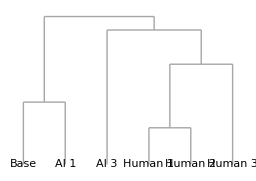

図1

表3

Base | AI 1 | Human 1 | Human 2 | Human 3 | AI 3
0 | 51 | 127 | 127 | 141 | 121
51 | 0 | 142 | 136 | 156 | 137
127 | 142 | 0 | 30 | 84 | 123
127 | 136 | 30 | 0 | 82 | 110
141 | 156 | 84 | 82 | 0 | 120
121 | 137 | 123 | 110 | 120 | 0

#### 修正の程度

次に、大学間で判定に差異があるかを確認する。まず表4に大学ごとのドキュメント数を示す。ドキュメントの修正の程度のヒストグラムを図2に示す。ヒストグラムの形状はいずれも同じ傾向に見えるが、さらにKruskal-Wallis法による検定を行った結果、P値は0.029であり有意差があると考えた方がよい。

表4

大学 1 | 26
大学 2 | 17
大学 3 | 31
大学 4 | 25

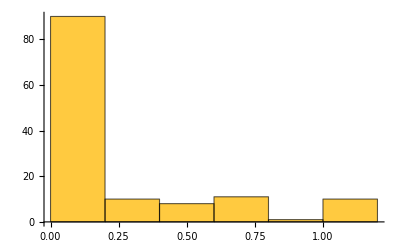
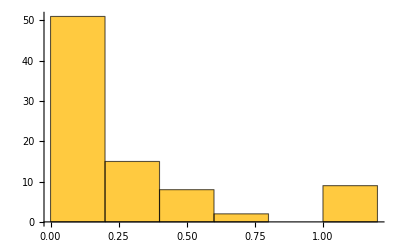
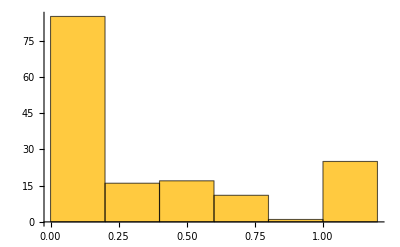
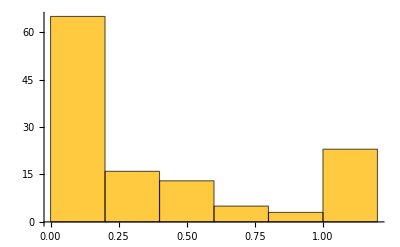
-Graphics-
大学 1 | -Graphics-
大学 2
-Graphics-
大学 3 | -Graphics-
大学 4

図2

#### どのような地名が抽出されているのか

地名であるかの決定

以降の評価を行うにあたり、地名であるかを決定するため、AIおよび人による混成判定の多数決により各箇所が地名であるかを決定した。この結果、mecabにより地名とされた141ターム（ユニーク）のうち、99タームが地名と判定された。一方、地名でないと判断されたターム（ユニーク）は45ターム、地名であると判定された場合も地名でないと判定された場合もあるタームは3タームであった。

抽出された地名の特徴

抽出された地名の中には1文字の「日」、「中」等の国名の略記が多く見られた。また、これらの中には「集」のようなあまり馴染みのないものもあったが、実際に存在する地名であった。しかし一方で地名でないにもかかわらず地名と判定されたものもあり、精度の視点からは低いものが多いと考えられる。

大学ごとの差異

次に、大学ごとに地名の出現に差があるかを、Dice係数をペアワイズで算出し確認した（表5）。係数の値は0.07から0.29と幅があり、大学ごとに嗜好があることが示唆される。

表5

(1. | 0.07 | 0.07 | 0.14
0.07 | 1. | 0.12 | 0.21
0.07 | 0.12 | 1. | 0.29
0.14 | 0.21 | 0.29 | 1.)

## 参照

https://www.lib.kagoshima-u.ac.jp/kgos/

https://www.lib.kagoshima-u.ac.jp/ja/about

https://kaken.nii.ac.jp/ja/